# Problem 2.22, Sakurai 3RD Edition

Write a computer program to animate the time dependence of an arbitrary linear combination of stationary states for the simple harmonic oscillator in one dimension . The animation should display the time dependence of both the wave function and the probability density distribution for finding the particle, both as a function of position . Check your animation by using pure eigenstates as input, and consider combinations that would approximate classical motion .

```mathematica
u[n_,x_]:=(1/(√π(2^n)Factorial[n]))HermiteH[n,x] Exp[-x^2]
```

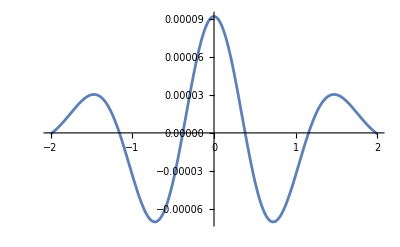

```mathematica
Plot[u[8, x],{x, -2,2}]
```

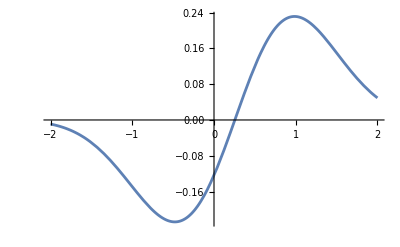

```mathematica
Plot[Sum[u[i,x],{i,1,4}], {x,-2,2}]
```